# An alternative expression for the current-to-rate gain function Φ(μ,σ) of LIF neurons

## Written by Maurizio Mattia, September 2022, Rome - Italy

## Script ploting Φ(μ,σ) shown in Fig. 1 of (Vinci & Mattia, 2024)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["LIFLibrary.m",Path-> NotebookDirectory[]]
```

```mathematica
Needs["NumericalCalculus`"]
```

Stationary Siegert-Ricciardi current-to-rate gain function [see Eq. (41) in (Vinci & Mattia, 2024)]:

```mathematica
Φ[Xr_,Xt_]:=1/MFPT[Xr,Xt];
```

## Using Parabolic Cylinder Functions

Not normalized (NN) eigenfunction ψ of the adjoint Fokker-Planck (FP) operator of LIF neurons:

```mathematica
ψNN[s_,x_]=  ⅇ^(x^2/2)ParabolicCylinderD[-s,-√2 x];
```

```mathematica
ψNN[s,Xr]/(ψNN[s,Xt]-ψNN[s,Xr])
```

(ⅇ^(Xr^2/2) ParabolicCylinderD[-s,-√2 Xr])/(-ⅇ^(Xr^2/2) ParabolicCylinderD[-s,-√2 Xr]+ⅇ^(Xt^2/2) ParabolicCylinderD[-s,-√2 Xt])

The current-to-rate gain function result to be the same as the normalized eigenfunction of the stationary mode (s = λ = 0),  which is given by [see Eq. (39) in (Vinci & Mattia, 2024)]:

```mathematica
ΦR[Xr_,Xt_]=FunctionExpand[Residue[ψNN[s,Xr]/(ψNN[s,Xt]-ψNN[s,Xr]),{s,0}]]
```

1/(ⅇ^(Xr^2/2) ParabolicCylinderD^(1,0)[0,-√2 Xr]-ⅇ^(Xt^2/2) ParabolicCylinderD^(1,0)[0,-√2 Xt])

This expression is provided by the Wolfram Encyclopedia of Mathematics:

```mathematica
D10[ν_,z_]=((-((2^(-1+ν/2) Sqrt[Pi] (Log[2]-2 PolyGamma[-ν]))/Gamma[(1-ν)/2])) Hypergeometric1F1[-(ν/2),1/2,z^2/2])/E^(z^2/4)+(((2^((ν-1)/2) Sqrt[Pi] (Log[2]-2 PolyGamma[-ν]) z)/Gamma[-(ν/2)]) Hypergeometric1F1[(1-ν)/2,3/2,z^2/2])/E^(z^2/4)-((2^(ν/2-1) Sqrt[Pi])/(E^(z^2/4) Gamma[(1-ν)/2])) Sum[(Pochhammer[-(ν/2),k] PolyGamma[k-ν/2] z^(2 k))/(k! Pochhammer[1/2,k] 2^k),{k,0,Infinity}]+((Sqrt[Pi] 2^((ν-1)/2) z)/(E^(z^2/4) Gamma[-(ν/2)])) Sum[(Pochhammer[(1-ν)/2,k] PolyGamma[k+(1-ν)/2] z^(2 k))/(k! Pochhammer[3/2,k] 2^k),{k,0,Infinity}]
```

(2^(1/2 (-1+ν)) ⅇ^(-z^2/4) √π z Hypergeometric1F1[(1-ν)/2,3/2,z^2/2] (Log[2]-2 PolyGamma[0,-ν]))/Gamma[-ν/2]-(2^(-1+ν/2) ⅇ^(-z^2/4) √π Hypergeometric1F1[-ν/2,1/2,z^2/2] (Log[2]-2 PolyGamma[0,-ν]))/Gamma[(1-ν)/2]+(2^(1/2 (-1+ν)) ⅇ^(-z^2/4) √π z (Hypergeometric1F1[1/2-ν/2,3/2,z^2/2] PolyGamma[0,(1-ν)/2]+Hypergeometric1F1^(1,0,0)[1/2-ν/2,3/2,z^2/2]))/Gamma[-ν/2]-(2^(-1+ν/2) ⅇ^(-z^2/4) √π (Hypergeometric1F1[-ν/2,1/2,z^2/2] PolyGamma[0,-ν/2]+Hypergeometric1F1^(1,0,0)[-ν/2,1/2,z^2/2]))/Gamma[(1-ν)/2]

```mathematica
Limit[D10[ν,z],ν->0]
```

Indeterminate

Actually there is an explicit expression for this limit contributed by Brychkov Yu.A. (2006) and found in The Wolfram Functions Site ( http://functions.wolfram.com/07.41.20.0005.01 ):

```mathematica
Derivative[1,0][ParabolicCylinderD][0,z]==((1/2) (-EulerGamma+Pi Erfi[z/Sqrt[2]]-Log[2]-z^2 HypergeometricPFQ[{1,1},{3/2,2},z^2/2]))/E^(z^2/4)
```

ParabolicCylinderD^(1,0)[0,z]==1/2 ⅇ^(-z^2/4) (-EulerGamma+π Erfi[z/(√2)]-z^2 HypergeometricPFQ[{1,1},{3/2,2},z^2/2]-Log[2])

```mathematica
D10ν0[z_]=1/2 ⅇ^(-z^2/4) (-EulerGamma+π Erfi[z/(√2)]-z^2 HypergeometricPFQ[{1,1},{3/2,2},z^2/2]-Log[2]);
```

From which we can rewrite the current-to-rate gain function Φ as

```mathematica
ΦR[Xr_,Xt_]=Simplify[1/(ⅇ^(Xr^2/2) D10ν0[-√2 Xr]-ⅇ^(Xt^2/2) D10ν0[-√2 Xt])]
```

-2/(π (Erfi[Xr]-Erfi[Xt])+2 Xr^2 HypergeometricPFQ[{1,1},{3/2,2},Xr^2]-2 Xt^2 HypergeometricPFQ[{1,1},{3/2,2},Xt^2])

```mathematica
Assuming[Xr∈Reals && Xt∈Reals,Limit[ⅇ^(Xr^2/2) D10[s,-√2 Xr]-ⅇ^(Xt^2/2)D10[s,-√2 Xt],s->0]]
```

lim_(s→0) (ⅇ^(Xr^2/2) (-(2^(1/2+1/2 (-1+s)) ⅇ^(-Xr^2/2) √π Xr Hypergeometric1F1[(1-s)/2,3/2,Xr^2] (Log[2]-2 PolyGamma[0,-s]))/Gamma[-s/2]-(2^(-1+s/2) ⅇ^(-Xr^2/2) √π Hypergeometric1F1[-s/2,1/2,Xr^2] (Log[2]-2 PolyGamma[0,-s]))/Gamma[(1-s)/2]-1/Gamma[-s/2]2^(1/2+1/2 (-1+s)) ⅇ^(-Xr^2/2) √π Xr (Hypergeometric1F1[1/2-s/2,3/2,Xr^2] PolyGamma[0,(1-s)/2]+Hypergeometric1F1^(1,0,0)[1/2-s/2,3/2,Xr^2])-(2^(-1+s/2) ⅇ^(-Xr^2/2) √π (Hypergeometric1F1[-s/2,1/2,Xr^2] PolyGamma[0,-s/2]+Hypergeometric1F1^(1,0,0)[-s/2,1/2,Xr^2]))/Gamma[(1-s)/2])-ⅇ^(Xt^2/2) (-(2^(1/2+1/2 (-1+s)) ⅇ^(-Xt^2/2) √π Xt Hypergeometric1F1[(1-s)/2,3/2,Xt^2] (Log[2]-2 PolyGamma[0,-s]))/Gamma[-s/2]-(2^(-1+s/2) ⅇ^(-Xt^2/2) √π Hypergeometric1F1[-s/2,1/2,Xt^2] (Log[2]-2 PolyGamma[0,-s]))/Gamma[(1-s)/2]-1/Gamma[-s/2]2^(1/2+1/2 (-1+s)) ⅇ^(-Xt^2/2) √π Xt (Hypergeometric1F1[1/2-s/2,3/2,Xt^2] PolyGamma[0,(1-s)/2]+Hypergeometric1F1^(1,0,0)[1/2-s/2,3/2,Xt^2])-(2^(-1+s/2) ⅇ^(-Xt^2/2) √π (Hypergeometric1F1[-s/2,1/2,Xt^2] PolyGamma[0,-s/2]+Hypergeometric1F1^(1,0,0)[-s/2,1/2,Xt^2]))/Gamma[(1-s)/2]))

## Fig. 1 in (Vinci & Mattia, 2024): plots of the current-to-rate gain function Φ(μ,σ)

Example neuron parameters assuming 0 mV for the resting potential and no absolute refractory period. See Fig. 1 in (Vinci  & Mattia, 2024). 
The following plot is for the standard Siegert-Ricciardi current-to-rate gain function [see Eq. (41) in (Vinci & Mattia, 2024)]

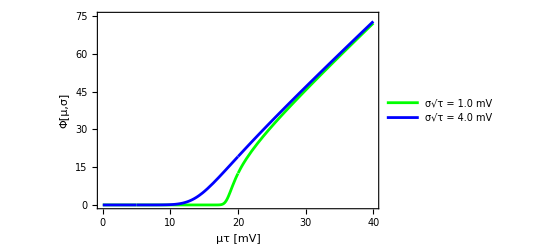

```mathematica
Module[{Vt,Vr,τ,στ},
τ=0.020; (* [s] Membrane potential decay time. *)
Vt=20.; (* [mV] Emission threshold. *)
Vr=0.; (* [mV] Reset potential. *)
στ={1,4};
hΦ=Plot[{Φ[(Vr-μτ)/στ[[1]],(Vt-μτ)/στ[[1]]]/τ,Φ[(Vr-μτ)/στ[[2]],(Vt-μτ)/στ[[2]]]/τ},{μτ,0,40},PlotStyle->{Green,Blue},PlotRange->{{0,40},{0,75}},Frame->True,FrameLabel->{"μτ [mV]","Φ[μ,σ]"},PlotLegends->{"σ√τ = 1.0 mV","σ√τ = 4.0 mV"}]
]
```

```mathematica
Export["PhiVsMuTau.pdf",hΦ,ImageResolution->200];
```

The following plot is for the novel expression of the current-to-rate gain function [Eq . (39) in (Vinci & Mattia, 2024)]

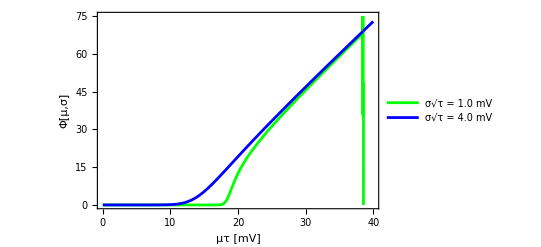

```mathematica
Module[{Vt,Vr,τ,στ},
τ=0.020; (* [s] Membrane potential decay time. *)
Vt=20.; (* [mV] Emission threshold. *)
Vr=0.; (* [mV] Reset potential. *)
στ={1,4};
Plot[{ΦR[(Vr-μτ)/στ[[1]],(Vt-μτ)/στ[[1]]]/τ,ΦR[(Vr-μτ)/στ[[2]],(Vt-μτ)/στ[[2]]]/τ},{μτ,0,40},PlotStyle->{Green,Blue},PlotRange->{{0,40},{0,75}},Frame->True,FrameLabel->{"μτ [mV]","Φ[μ,σ]"},PlotLegends->{"σ√τ = 1.0 mV","σ√τ = 4.0 mV"}]
]
```

```mathematica
Export["PhiVsMuTauParCylResidue.pdf",hΦRD,ImageResolution->200];
```

## Φ(μ,σ) computed using Confluent Hypergeometric Functions [not used in Fig. 1 of (Vinci & Mattia,2024)]

Not normalized (NN) eigenfunction ψ of the adjoint Fokker-Planck (FP) operator of LIF neurons:

```mathematica
ψNN[s_,x_]=Hypergeometric1F1[s/2,1/2,x^2]/Gamma[(s+1)/2]+2x Hypergeometric1F1[(1+s)/2,3/2,x^2]/Gamma[s/2];
```

The current-to-rate gain function result to be the same as the normalized eigenfunction of the stationary mode (s = λ = 0),  which is given by:

```mathematica
ΦR[Xr_,Xt_]=Residue[ψNN[s,Xr]/(ψNN[s,Xt]-ψNN[s,Xr]),{s,0}]
```

-2/(π Erfi[Xr]-π Erfi[Xt]+Hypergeometric1F1^(1,0,0)[0,1/2,Xr^2]-Hypergeometric1F1^(1,0,0)[0,1/2,Xt^2])

```mathematica
FunctionExpand[%]
```

-2/(π Erfi[Xr]-π Erfi[Xt]+Hypergeometric1F1^(1,0,0)[0,1/2,Xr^2]-Hypergeometric1F1^(1,0,0)[0,1/2,Xt^2])

```mathematica
FunctionExpand[Derivative[1,0,0][Hypergeometric1F1][0,1/2,Xr^2]]
```

Hypergeometric1F1^(1,0,0)[0,1/2,Xr^2]

This expression is provided by the Wolfram Encyclopedia of Mathematics:

```mathematica
M100[a_,b_,z_]=Sum[((Pochhammer[a,k] PolyGamma[a+k])/(k! Pochhammer[b,k])) z^k,{k,0,Infinity}]-PolyGamma[a] Hypergeometric1F1[a,b,z]
```

Hypergeometric1F1^(1,0,0)[a,b,z]

```mathematica
Table[{k,Pochhammer[0,k]},{k,0,3}]
```

{{0,1},{1,0},{2,0},{3,0}}

```mathematica
Table[{k,PolyGamma[0+k]},{k,0,3}]
```

{{0,ComplexInfinity},{1,-EulerGamma},{2,1-EulerGamma},{3,3/2-EulerGamma}}

```mathematica
Table[{k,Pochhammer[1/2,k]},{k,0,3}]
```

{{0,1},{1,1/2},{2,3/4},{3,15/8}}

```mathematica
Table[{k,(Pochhammer[0,k] z^k)/(k!Pochhammer[1/2,k])},{k,0,3}]
```

{{0,1},{1,0},{2,0},{3,0}}

```mathematica
Hypergeometric1F1[0,1/2,z]
```

1

```mathematica
Limit[M100[a,1/2,Xr^2],a->0]
```

Hypergeometric1F1^(1,0,0)[0,1/2,Xr^2]

```mathematica
FunctionExpand[Limit[M100[a,1/2,Xr^2]-M100[a,1/2,Xt^2],a->0]]
```

Hypergeometric1F1^(1,0,0)[0,1/2,Xr^2]-Hypergeometric1F1^(1,0,0)[0,1/2,Xt^2]

```mathematica
N[Derivative[1,0,0][Hypergeometric1F1][0,1/2,-20.1]]
```

-4.93834